```mathematica
kk2=Select[Keys[treeForm5],MemberQ[{v13x24x5+v13x25x4+v13x2x4x5,v13x24x5+v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5

},(treeForm5[#,"colofour"])]&]
```

{20695,35977}

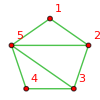
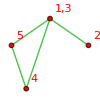
{-Graphics-{20695→-Graphics-v1x2x3x4x5+-Graphics-v1x24x3x5+-Graphics-v13x2x4x5+-Graphics-v13x24x5+-Graphics-v14x2x3x5,4}Planar contraction (late),-Graphics-{35977→-Graphics-v13x2x4x5+-Graphics-v13x24x5+-Graphics-v13x25x4,3}Planar contraction (late)}

```mathematica
Table[CosyPrint5[k,stubbornForm5]/.repcolofour5base,{k,kk2}]
```

```mathematica
CosyPrint5[27610,stubbornForm5]
```

```mathematica
kk=Select[Keys[treeForm5],MemberQ[{v14x235+v14x23x5,
v14x235+v1x235x4,
v13x245+v1x245x3,
v13x245+v13x2x45,
v135x2x4+v15x2x3x4,
v135x24+v135x2x4,
v134x2x5+v1x2x34x5,
v134x25+v134x2x5,
v15x24x3+v15x2x3x4,
v14x23x5+v1x23x4x5,
v124x3x5+v12x3x4x5,
v124x35+v124x3x5,
v135x24+v15x24x3,
v1x235x4+v1x23x4x5,
v12x35x4+v12x3x4x5,
v1x25x34+v1x2x34x5,
v1x245x3+v1x2x3x45,
v124x35+v12x35x4,
v134x25+v1x25x34,
v13x2x45+v1x2x3x45

},(treeForm5[#,"colofour"])]&]
```

{20785,20812,22964,23072,23689,23770,27580,27610,29417,29506,29737,30172,31924,35978,36736,38254,46939,46942,49204,51472}

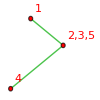
-Graphics-{27610→v14x235+v1x235x4,3/2}Planar contraction (late)

```mathematica
CosyPrint5[27610,stubbornForm5]
```

```mathematica
withRelations5[27160]
```

Missing[KeyAbsent,27160]

```mathematica
treeForm5[27160,"colofour"]
```

Missing[KeyAbsent,27160]

```mathematica
Length[stubbornForm5]
```

1895

```mathematica
Select[Keys[stubbornForm5],#==27160&]
```

{}

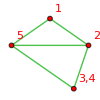
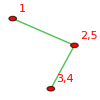
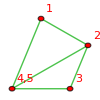
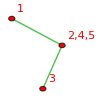
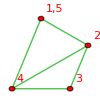
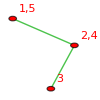
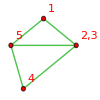
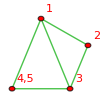
{-Graphics-{20785→v134x2x5+v1x2x34x5,2}Planar contraction (late),-Graphics-{20812→v134x25+v1x25x34,3/2}Planar contraction (late),-Graphics-{22964→v13x2x45+v1x2x3x45,2}Planar contraction (late),-Graphics-{23072→v13x245+v1x245x3,3/2}Planar contraction (late),-Graphics-{23689→v135x2x4+v15x2x3x4,2}Planar contraction (late),-Graphics-{23770→v135x24+v15x24x3,3/2}Planar contraction (late),-Graphics-{27580→v14x23x5+v1x23x4x5,2}Planar contraction (late),-Graphics-{27610→v14x235+v1x235x4,3/2}Planar contraction (late),-Graphics-{29417→v1x245x3+v1x2x3x45,2}Planar contraction (late),-Graphics-{29506→v1x25x34+v1x2x34x5,2}Planar contraction (late),-Graphics-{29737→v1x235x4+v1x23x4x5,2}Planar contraction (late),-Graphics-{30172→v15x24x3+v15x2x3x4,2}Planar contraction (late),-Graphics-{31924→v14x235+v14x23x5,3/2}Planar contraction (late),-Graphics-{35978→v13x245+v13x2x45,3/2}Planar contraction (late),-Graphics-{36736→v135x24+v135x2x4,3/2}Planar contraction (late),-Graphics-{38254→v134x25+v134x2x5,3/2}Planar contraction (late),-Graphics-{46939→v124x3x5+v12x3x4x5,2}Planar contraction (late),-Graphics-{46942→v124x35+v12x35x4,3/2}Planar contraction (late),-Graphics-{49204→v12x35x4+v12x3x4x5,2}Planar contraction (late),-Graphics-{51472→v124x35+v124x3x5,3/2}Planar contraction (late)}

```mathematica
Table[CosyPrint5[k,treeForm5],{k,kk}]
```

```mathematica
SetToNodePicture[set_,n_]:=Block[{circleCoord=10*CircleLayout[n],prim={Disk[{0,0},.01]}},
prim=Join[{Disk[{1/2,1/2},0.5]},Table[Disk[circleCoord[[k]],0.5,{-(2Pi+2)/n*k,-(2Pi-2)/n*k}],{k,set}]];
Graphics[prim]
]
```

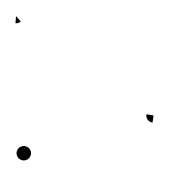

```mathematica
SetToNodePicture[{1,2},5]
```

```mathematica
CircleLayout[5]
```

{{0,1},{√(5/8+(√5)/8),1/4 (-1+√5)},{√(5/8-(√5)/8),1/4 (-1-√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)},{-√(5/8+(√5)/8),1/4 (-1+√5)}}

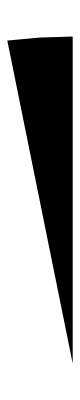
{-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Disk[{0,0},0.1,{Pi/2,1.1Pi/2}]],{k,{1,2}}]
```

```mathematica
Disk[{0,0},1,{Pi/4,3Pi/4}]
```

Disk[{0,0},1,{π/4,(3 π)/4}]

```mathematica
MyPlanar2[assoc_,key_]:=Block[
{item=assoc[key], emb, pos=Association[],posOuter=Association[], length,lines={},sets,res,line1,line2,crit, found=False,mat,i,j,x,y, challenge},
x=Symbol["abcx"<>ToString[key]];
y=Symbol["abcy"<>ToString[key]];
emb=GraphEmbedding[item["graph"]];
length=Length[Flatten[item["vertexsets"]]];
mat=item["matrix"];
i=1;
Table[
Table[
pos[v]=IntegerPart[100*Round[emb[[i]],0.01]];
,{v,set}
];
i++
,{set,item["vertexsets"]}
];
Table[posOuter[k]=200*{Cos[(2π/length )(length-k+1)+Pi/2],Sin[(2π/length )(k-1)+Pi/2]},{k,length}];
Table[crit=Line[{pos[k],posOuter[k]}];lines=Append[ lines,crit],{k,length}];

Table[
i=Min[item["vertexsets"][[e[[1]]]]];
j=Min[item["vertexsets"][[e[[2]]]]];
crit=Line[{pos[i],pos[j]} ];lines=Append[ lines,crit],
{e,EdgeList[item["graph"]]}
];

lines
]
```

```mathematica
MyPlanar2[stubbornForm5,31708]
```

{Line[{{0,100},{0,200}}],Line[{{95,31},{200 √(5/8+(√5)/8),50 (-1+√5)}}],Line[{{59,-81},{200 √(5/8-(√5)/8),50 (-1-√5)}}],Line[{{0,100},{-200 √(5/8-(√5)/8),50 (-1-√5)}}],Line[{{-95,31},{-200 √(5/8+(√5)/8),50 (-1+√5)}}],Line[{{95,31},{59,-81}}],Line[{{95,31},{-95,31}}],Line[{{95,31},{0,100}}],Line[{{59,-81},{0,100}}],Line[{{-95,31},{0,100}}]}

```mathematica
MyPlanar[stubbornForm5,31708]
```

False

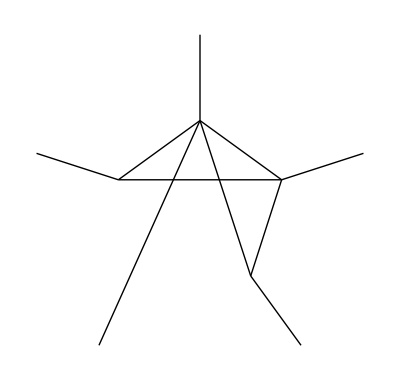

```mathematica
Graphics[MyPlanar2[stubbornForm5,31708]]
```

```mathematica
NSolve[0<x<59&&-81<y<100&&81+y==-181/59 (-59+x),{x,y}]
```

NSolve::svars: Equations may not give solutions for all "solve" variables.

{{x→ConditionalExpression[0.00552486 (5900.-59. y),-81.<y<100.]}}